# 实验习题5

## 工科数学分析——数学实验

## 题1

```mathematica
f[x_] := Sin[x^2];
a=0;b=Pi/2;n=100;
```

```mathematica
N[∑_(k=1)^n ((b-a) f((((k-1)+0.5) (b-a))/n+a))/n]
```

0.828142

可见∫_0^(π/2) sin(x^2)ⅆx的黎曼和为0.828142。

## 题2

```mathematica
Clear[x,a,b];
f[x_] := Sin[x^2];
```

### 用梯形法计算定积分的近似值

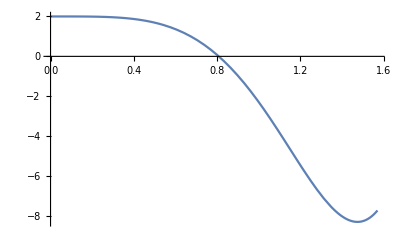

```mathematica
Plot[f''[x],{x,0,Pi/2}]
```

```mathematica
FindMaximum[{f''[x],0<=x<=Pi/2},{x,Pi/4}]
```

{2.,{x→0.00821245}}

```mathematica
a=0;b=Pi/2;m2=2;delta=10^(-4);n0=100;
```

```mathematica
t(n_):=((b-a) (∑_(i=1)^(n-1) f((i (b-a))/n+a)+1/2 (f(a)+f(b))))/n;
Do[Print[n,"    ",N[t[n],8]];If[(b-a)^3/(12*n^2)*m2<delta,Break[],If[n==n0,Print["迭代次数不能满足精度要求。"]]],
{n,n0}]
```

1    0.49029733

2    0.69947699

3    0.77101887

4    0.79620809

5    0.80777297

6    0.81402084

7    0.81777512

8    0.82020628

9    0.8218705

10    0.8230596

11    0.82393868

12    0.82460689

13    0.82512667

14    0.82553894

15    0.82587144

16    0.8261435

17    0.82636893

18    0.82655782

19    0.82671764

20    0.82685409

21    0.82697149

22    0.82707325

23    0.82716201

24    0.82723991

25    0.82730864

26    0.8273696

27    0.8274239

28    0.82747249

29    0.82751614

30    0.82755549

31    0.8275911

32    0.82762342

33    0.82765285

34    0.82767971

35    0.82770431

36    0.82772689

37    0.82774766

38    0.82776681

39    0.82778451

40    0.82780089

41    0.82781609

42    0.82783022

43    0.82784337

44    0.82785564

45    0.8278671

46    0.82787782

47    0.82788786

48    0.82789728

49    0.82790613

50    0.82791446

51    0.8279223

52    0.82792969

53    0.82793667

54    0.82794326

55    0.8279495

56    0.8279554

57    0.827961

58    0.82796631

59    0.82797135

60    0.82797614

61    0.8279807

62    0.82798504

63    0.82798918

64    0.82799312

65    0.82799688

66    0.82800048

67    0.82800391

68    0.82800719

69    0.82801033

70    0.82801334

71    0.82801622

72    0.82801898

73    0.82802163

74    0.82802417

75    0.82802661

76    0.82802896

77    0.82803121

78    0.82803338

79    0.82803547

80    0.82803748

81    0.82803941

可见用梯形法计算∫_0^(π/2) sin(x^2)ⅆx的近似值为0.82803941，误差不超过10^(-4)。

### 用抛物线法计算定积分的近似值

```mathematica
D[f[x],{x,4}]
```

-48 x^2 Cos[x^2]-12 Sin[x^2]+16 x^4 Sin[x^2]

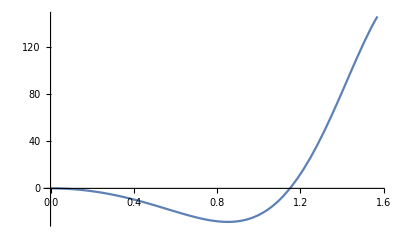

```mathematica
Plot[-48 x^2 Cos[x^2]-12 Sin[x^2]+16 x^4 Sin[x^2],{x,0,Pi/2}]
```

```mathematica
m4=D[f[x],{x,4}]/.x->Pi/2;k0=100;
```

```mathematica
p[k_]:=(b-a)/(6*k)*(f[a]+f[b]+4*∑_(i=1)^k (f[a+(2i-1)*(b-a)/(2k)])+2*∑_(i=1)^(k-1) (f[a+2*i*(b-a)/(2k)]));
```

```mathematica
Do[Print[k,"   ",N[p[k]]];If[m4*(b-a)^5/(180*(2*k)^4)<delta,Break[],If[k==k0,Print["迭代次数不能满足精度要求。"]]]
,{k,k0}]
```

1   0.769204

2   0.828452

3   0.828355

4   0.828206

5   0.828155

6   0.828136

7   0.828127

8   0.828123

9   0.82812

可见用抛物线法计算∫_0^(π/2) sin(x^2)ⅆx的近似值为0.828120，误差不超过10^(-4)。